The first part of my project was understanding some of the basics of Mathematica. I started out by trying to define a function called f as equal to cos(x).

```mathematica
f[x_]:= Cos[x]
```

SetDelayed::write: Tag Times in (cos x)[x_] is Protected.

$Failed

```mathematica
f[x_]:=Cos[x]
```

SetDelayed::write: Tag Times in (cos x)[x_] is Protected.

```mathematica
?f
```

Global`f

After failing the first to times I tried defining cos(x) as a variable called expression. I found that this worked. I later learned that the reason that defining cosine as a variable didn’t work was because it was a built-in function.

```mathematica
expression :=Cos[x]
```

```mathematica
?expression
```

Global`expression

expression:=Cos[x]

Next I looked at how I can plot different functions. I thought that this would be useful when proving that a Taylor series was an approximation of another function. For this I used the built-in plot function.

```mathematica
Plot[expression, {x, -2π, 2π}]
```

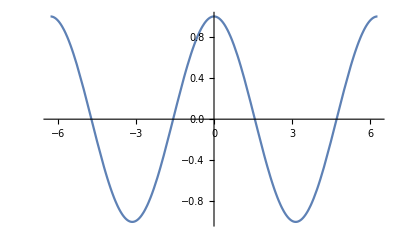
```mathematica
-Graphics-
Clear[expression]
```

-Graphics-

```mathematica
f := Cos[x]
```

```mathematica
?f
```

Global`f

f:=Cos[x]

Here I worked on some ways that I could interact with functions. I thought that this would be a useful tool if I want to look at how close my approximations get as I increase the number of terms in my Taylor series. I used the built-in Manipulate function to do this. This failed the first two times because I needed to input a function instead of a variable so that I could give Mathematica the bounds of my graph.

```mathematica
Manipulate[Plot[f, {x, -2π, 2π}]]
```

```mathematica
f[3]
```

```mathematica
Plot[Cos[x],{x,-10,10}]
```

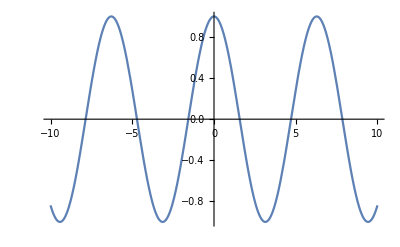
```mathematica
-Graphics-
Manipulate[Plot[Cos[x y],{x,-10,10}],{y,-10,10}]
```

At this point I decided to try creating a Taylor series. I used the Sum function to create my Taylor series. My variables were x and a. X represented the x axis while a was the size of the series. To model my series I thought it would be useful to use a 3 dimensional graphic because I have two variables in my equation. This was unsuccessful so I moved on.

```mathematica
g[x_, a_] := Sum[((((-1)^i)*(x^(2i)))/(2n)!), {i, 0, a}]
Plot3D[g, {x, -10, 10}, {y, -10, 10}]
```

```mathematica
-Graphics3D-
Manipulate[Plot[g[x,top], {x,0, 9}], {top, 0, 30}]
```

```mathematica
-Graphics3D-
Manipulate[Plot[g[x,top],{x,0,9}],{top,0,10}]
```

```mathematica
g[0, 100]
```

Power::indet: Indeterminate expression 0^0 encountered.

General::ivar: 0.000183857 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: 0.000183857 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: 0.000183857 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: 0.000183857 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

```mathematica
Indeterminate
Clear[g]
```

```mathematica
Clear[f]
```

Here is where I started my exploration of the Taylor series. I input the Taylor series of cosine as f of x. I then plotted f of x. I also created a function called h of x which was equal to x squared. I did this to create a new function called g of x that was equal to h of f of x.

```mathematica
f[x_,y_] := Sum[((-1)^n x^(2 n))/((2 n)!), {n, 0, y}]
```

```mathematica
Plot[{f[x, Infinity], Cos[x]}, {x, -2 Pi, 2 Pi}]
```

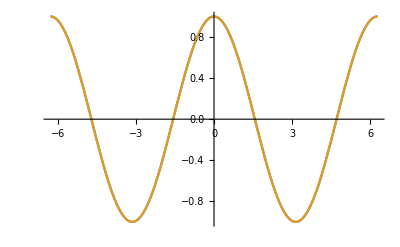

```mathematica
h[x_]:=x^2
```

```mathematica
Plot[h[x], {x, 0, 9}]
```

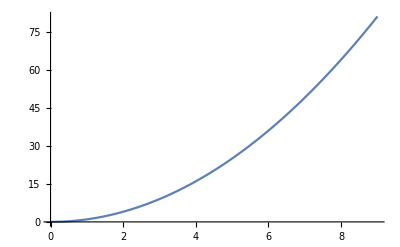

```mathematica
g[x_,y_]:=h[f[x, y]]
```

Below I created the function i of x which was the Taylor series of g of x. The goal of doing this was to prove that g of x is equal to its Taylor series.

```mathematica
i[x_,y_]:=Sum[D[g[0],{x,n}]/(n!) x^n, {n, 1, y}]
```

i[x_,y_]:=∑_(n=0)^y (N[g[0],{x,n}] x^n)/(n!)

g[x_]=Cos[x]^2

I first tried to prove that i of x was equal to g of x using plots. I attempted to use a 3 dimensional graph to show that the two functions were equal as y approached infinity. I found that the graphs were difficult to interpret and I did not think that it would be as rigorous as some other methods.

```mathematica
Plot3D[{g[x,y],i[x,y]},{x,-10, 10},{y,0,10}]
```

Power::indet: Indeterminate expression 0^0 encountered.

N::precsm: Requested precision -9.99857 is smaller than $MinPrecision. Using $MinPrecision instead.

NSum::wprec: Value of option WorkingPrecision -> 0``-1.2041199826559248 is not a positive machine-sized real or integer.

Power::indet: Indeterminate expression 0.^0 encountered.

Power::indet: Indeterminate expression 0.^0. encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

NSum::wprec: Value of option WorkingPrecision -> 0. is not a positive machine-sized real or integer.

N::precsm: Requested precision -8.57 is smaller than $MinPrecision. Using $MinPrecision instead.

NSum::wprec: Value of option WorkingPrecision -> 0``-1.2041199826559248 is not a positive machine-sized real or integer.

General::stop: Further output of NSum::wprec will be suppressed during this calculation.

N::precsm: Requested precision -7.14143 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

NSum::precw: The precision of the argument function ((-1.)^n 0^0) is less than WorkingPrecision (16.).

NSum::nsnum: Summand (or its derivative) Indeterminate is not numerical at point n = 46661.

NSum::precw: The precision of the argument function ((-1.)^n 0^0) is less than WorkingPrecision (16.).

NSum::nsnum: Summand (or its derivative) Indeterminate is not numerical at point n = 46661.

NSum::precw: The precision of the argument function ((-1.)^n 0^0) is less than WorkingPrecision (16.).

General::stop: Further output of NSum::precw will be suppressed during this calculation.

NSum::nsnum: Summand (or its derivative) Indeterminate is not numerical at point n = 46661.

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 (-1.)^n ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[%98,ImageSize->Full]
```

-Graphics3D-

```mathematica
Show[%101,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[{g[x,a],i[x,a]},{x,-10, 10}],{a, 0, 10}]
```

General::ivar: -9.99959 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,3.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,3.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: -9.99917 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99917 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::ivar: 0 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,0.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,1.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

After trying to use a 3 dimensional plot, I moved on to trying to prove the Taylor series by expanding the function. Because both functions are summations it is possible to expand them and prove that they are equal if each of their terms is equal as each function approaches infinity. This failed at first because I had input the functions incorrectly. The main problem at first was that Mathematica would not numerically evaluate the nth derivative. I fixed this by editing the syntax to accommodate numeric evaluations.

```mathematica
Manipulate[Expand[g[x,n]],{n,0,20}]
```

```mathematica
Expand[i[x,10]]
```

Power::indet: Indeterminate expression 0^0 encountered.

D::iti: Invalid index 1 in iterator {1,0,∞}.

Power::indet: Indeterminate expression 0^0 encountered.

D::iti: Invalid index 2 in iterator {2,0,∞}.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

D::iti: Invalid index 3 in iterator {3,0,∞}.

General::stop: Further output of D::iti will be suppressed during this calculation.

0

```mathematica
x N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,1}]+1/2 x^2 N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,2}]+1/6 x^3 N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,3}]+1/24 x^4 N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,4}]+1/120 x^5 N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,5}]+1/720 x^6 N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,6}]+(x^7 N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,7}])/5040+(x^8 N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,8}])/40320+(x^9 N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,9}])/362880+(x^10 N[(∑_(n=0)^∞ ((-1)^n 0^(2 n))/((2 n)!))^2,{x,10}])/3628800
```

```mathematica
w[x_,y_]:=Sum[N[g[0],{x,n}]/(n!) x^n, {n, 1, y}]
```

```mathematica
Manipulate[Expand[w[x,t]],{t,0,20}]
```

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

Power::indet: Indeterminate expression 0^0 encountered.

N::precbd: Requested precision x is not a machine-sized real number between $MinPrecision and $MaxPrecision.

General::stop: Further output of N::precbd will be suppressed during this calculation.

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

```mathematica
r[x_,y_]:=Sum[D[Cos[0]^2,{x,n}]/(n!) x^n, {n, 1, y}]
Manipulate[Expand[r[x,t]],{t,0,20}]
```

```mathematica
Evaluate[D[Cos[x]^2,{x,4}],0]
```

```mathematica
Sequence[8 Cos[x]^2-8 Sin[x]^2,0]
```

```mathematica
D[Cos[x]^2, {x, 4}] /. {x -> 0}
```

8

```mathematica
n=8
D[Cos[x]^2, {x, n}] /. {x -> 0}
```

8

128

Below is the proof of the Taylor series. By expanding the summations of i of x and g of x into their terms, I have shown that they are equal at all terms. I have also shown that the functions are equal as the size of their expansion approaches infinity using the SameQ function.

```mathematica
i[x_,y_]:=Sum[(D[Cos[x]^2, {x, n}] /. {x -> 0})/(n!) x^n, {n, 0, y}]
Manipulate[Expand[i[x,t]],{t,0,20}]
```

```mathematica
Manipulate[Expand[g[x,t]],{t,0,20}]
```

```mathematica
SameQ[g[x,Infinity] == i[x,Infinity]]
```

True